## Pump and probe both are linearly polarized and orthogonal i.e., all σ^(+/-) components are active. This happens because the quantization axis in along z.

```mathematica
Clear[raa,rab,rac,rad,rae,raf,rag,rah,rai,raj,rak,ral,ram,ran,rao,rap,rba,rbb,rbc,rbd,rbe,rbf,rbg,rbh,rbi,rbj,rbk,rbl,rbm,rbn,rbo,rbp,rca,rcb,rcc,rcd,rce,rcf,rcg,rch,rci,rcj,rck,rcl,rcm,rcn,rco,rcp,rda,rdb,rdc,rdd,rde,rdf,rdg,rdh,rdi,rdj,rdk,rdl,rdm,rdn,rdo,rdp,rea,reb,rec,red,ree,ref,reg,reh,rei,rej,rek,rel,rem,ren,reo,rep,rfa,rfb,rfc,rfd,rfe,rff,rfg,rfh,rfi,rfj,rfk,rfl,rfm,rfn,rfo,rfp,rga,rgb,rgc,rgd,rge,rgf,rgg,rgh,rgi,rgj,rgk,rgl,rgm,rgn,rgo,rgp,rha,rhb,rhc,rhd,rhe,rhf,rhg,rhh,rhi,rhj,rhk,rhl,rhm,rhn,rho,rhp,ria,rib,ric,rid,rie,rif,rig,rih,rii,rij,rik,ril,rim,rin,rio,rip,rja,rjb,rjc,rjd,rje,rjf,rjg,rjh,rji,rjj,rjk,rjl,rjm,rjn,rjo,rjp,rka,rkb,rkc,rkd,rke,rkf,rkg,rkh,rki,rkj,rkk,rkl,rkm,rkn,rko,rkp,rla,rlb,rlc,rld,rle,rlf,rlg,rlh,rli,rlj,rlk,rll,rlm,rln,rlo,rlp,rma,rmb,rmc,rmd,rme,rmf,rmg,rmh,rmi,rmj,rmk,rml,rmm,rmn,rmo,rmp,rna,rnb,rnc,rnd,rne,rnf,rng,rnh,rni,rnj,rnk,rnl,rnm,rnn,rno,rnp,roa,rob,roc,rod,roe,rof,rog,roh,roi,roj,rok,rol,rom,ron,roo,rop,rpa,rpb,rpc,rpd,rpe,rpf,rpg,rph,rpi,rpj,rpk,rpl,rpm,rpn,rpo,rpp,Rpl,Rph,Rcl,Rch,theta,x1,z,ew,v,δc,δp,B,Rp,Rc,k,g1,g2,Γ,γw,table2];
kB=1.38*10^-23;T=273+36;c=3*10^8;d=2.537 10^(-29);h=2 Pi 1.0545718 10^-34;ep0=8.854 10^-12;
mass=87*1.6*10^-27;
Γ=6 10^6;
MB[velocity_]:=Evaluate[Sqrt[mass/(2 Pi kB T)] Exp[-mass velocity^2/(2 kB T)]];

dia=0.2;area=Pi dia^2/4;
Pc=5;Pp=0.01;
Ic=Pc/area;Ip=Pp/area;
Isat=2.5;
Rc=Γ Sqrt[Ic/2/Isat];
Rp=Γ Sqrt[Ip/2/Isat];
caj=√(5/4); 
cal=√(1/4);
can=√(1/24);
cai=-√(5/24);
cam=-√(1/8);
cbi=-√(5/24);
cbk=√(5/24);
cbm=√(1/8);
cbo=√(1/8);
cbj=0;
cbn=-√(1/6);
ccj=-√(5/24);
 ccn=√(1/24);
ccp=√(1/4);
cck=√(5/24) ;
cco=- √(1/8) ;
 cdi=√(1/20) ;
cdm=√(1/12) ;
cdl= -√(1/6);
cel=- √(1/12) ;
cej=√(1/40) ;
cei=√(1/40) ;
cen=√(1/8) ;
cem= - √(1/24) ;
cfi=√(1/120);
cfk=√(1/120);
cfm=-√(1/8);
cfo=√(1/8);
cfj=√(1/30);
cfn=0;
cgj=√(1/40);
cgn=-√(1/8);
cgp=√(1/12);
cgk=√(1/40);
cgo=√(1/24);
chk=√(1/20);
cho=-√(1/12);
chp=√(1/6);
g1=0.70*10^6;
g2=0.93*10^6;
B=45;
γb=0.2 10^6;
γd=1/625 γb;
γw=1000;
k=1/780*10^9;
Δe=157*10^6;
δp=0;
Rpl=  Rp /√2+0*Sin[theta-Pi/4];
Rph= Rp /√2+0*Rp Cos[theta-Pi/4];
Rcl= Rc /√2 +0* Cos[theta-Pi/4];
Rch= Rc /√2  +0*Sin[theta-Pi/4];
theta=0;
r={{raa,rab,rac,rad,rae,raf,rag,rah,rai,raj,rak,ral,ram,ran,rao,rap},{rba,rbb,rbc,rbd,rbe,rbf,rbg,rbh,rbi,rbj,rbk,rbl,rbm,rbn,rbo,rbp},{rca,rcb,rcc,rcd,rce,rcf,rcg,rch,rci,rcj,rck,rcl,rcm,rcn,rco,rcp},{rda,rdb,rdc,rdd,rde,rdf,rdg,rdh,rdi,rdj,rdk,rdl,rdm,rdn,rdo,rdp},{rea,reb,rec,red,ree,ref,reg,reh,rei,rej,rek,rel,rem,ren,reo,rep},{rfa,rfb,rfc,rfd,rfe,rff,rfg,rfh,rfi,rfj,rfk,rfl,rfm,rfn,rfo,rfp},{rga,rgb,rgc,rgd,rge,rgf,rgg,rgh,rgi,rgj,rgk,rgl,rgm,rgn,rgo,rgp},{rha,rhb,rhc,rhd,rhe,rhf,rhg,rhh,rhi,rhj,rhk,rhl,rhm,rhn,rho,rhp},{ria,rib,ric,rid,rie,rif,rig,rih,rii,rij,rik,ril,rim,rin,rio,rip},{rja,rjb,rjc,rjd,rje,rjf,rjg,rjh,rji,rjj,rjk,rjl,rjm,rjn,rjo,rjp},{rka,rkb,rkc,rkd,rke,rkf,rkg,rkh,rki,rkj,rkk,rkl,rkm,rkn,rko,rkp},{rla,rlb,rlc,rld,rle,rlf,rlg,rlh,rli,rlj,rlk,rll,rlm,rln,rlo,rlp},{rma,rmb,rmc,rmd,rme,rmf,rmg,rmh,rmi,rmj,rmk,rml,rmm,rmn,rmo,rmp},{rna,rnb,rnc,rnd,rne,rnf,rng,rnh,rni,rnj,rnk,rnl,rnm,rnn,rno,rnp},{roa,rob,roc,rod,roe,rof,rog,roh,roi,roj,rok,rol,rom,ron,roo,rop},{rpa,rpb,rpc,rpd,rpe,rpf,rpg,rph,rpi,rpj,rpk,rpl,rpm,rpn,rpo,rpp}};
hi= {{0,0,0,0,0,0,0,0,0,- caj Rph/2,0,- cal Rpl/2,0,- can Rph/2,0,0},{0,0,0,0,0,0,0,0,- cbi Rpl/2,0,- cbk Rph/2,0,- cbm Rpl/2,0,- cbo Rph/2,0},{0,0,0,0,0,0,0,0,0,- ccj Rpl/2,0,0,0,- ccn Rpl/2,0,- ccp Rph/2},{0,0,0,0,0,0,0,0,- cdi Rch/2,0,0,0,- cdm Rch/2,0,0,0},{0,0,0,0,0,0,0,0,0,- cej Rch/2,0,- cel Rcl/2,0,- cen Rch/2,0,0},{0,0,0,0,0,0,0,0,- cfi Rcl/2,0,- cfk Rch/2,0,- cfm Rcl/2,0,- cfo Rch/2,0},{0,0,0,0,0,0,0,0,0,- cgj Rcl/2,0,0,0,- cgn Rcl/2,0,- cgp Rch/2},{0,0,0,0,0,0,0,0,0,0,- chk Rcl/2,0,0,0,- cho Rcl/2,0},{0,- cbi Rpl/2,0,- cdi Rch/2,0,- cfi Rcl/2,0,0,0,0,0,0,0,0,0,0},{- caj Rph/2,0,- ccj Rpl/2,0,- cej Rch/2,0,- cgj Rcl/2,0,0,0,0,0,0,0,0,0},{0,- cbk Rph/2,0,0,0,- cfk Rch/2,0,- chk Rcl/2,0,0,0,0,0,0,0,0},{- cal Rpl/2,0,0,0,- cel Rcl/2,0,0,0,0,0,0,0,0,0,0,0},{0,- cbm Rpl/2,0,- cdm Rch/2,0,- cfm Rcl/2,0,0,0,0,0,0,0,0,0,0},{- can Rph/2,0,- ccn Rpl/2,0,- cen Rch/2,0,- cgn Rcl/2,0,0,0,0,0,0,0,0,0},{0,- cbo Rph/2,0,0,0,- cfo Rch/2,0,- cho Rcl/2,0,0,0,0,0,0,0,0},{0,0,- ccp Rph/2,0,0,0,- cgp Rch/2,0,0,0,0,0,0,0,0,0}};
h0={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,δp-δc,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,-Δe+δp-k v,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,δp-k v}};
hb=B {{+ g1 ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,- g1,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,- 2 g1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,- g1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,g1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2 g1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,- g2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,g2,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,- 2 g2,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,- g2,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,g2,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 g2}};
h=hi+h0+hb;
de= Γ{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};
repop=Γ {{cai^2 rii +caj^2 rjj +cal^2 rll+cam^2 rmm+can^2 rnn,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,cbi^2 rii+cbj^2 rjj +cbk^2 rkk+cbm^2 rmm+cbn^2 rnn +cbo^2 roo,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,ccj^2 rjj +cck^2 rkk +ccn^2 rnn+cco^2 roo +ccp^2 rpp,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,cdi^2 rii+cdl^2 rll +cdm^2 rmm,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,cei^2 rii +cej^2 rjj +cel^2 rll+cem^2 rmm +cen^2 rnn,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,cfi^2 rii+cfj^2 rjj +cfk^2 rkk+cfm^2 rmm+cfn^2 rnn +cfo^2 roo,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,cgj^2 rjj +cgk^2 rkk +cgn^2 rnn+cgo^2 roo+cgp^2 rpp,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,chk^2 rkk+cho^2 roo +chp^2 rpp,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
gde=γw r;
commutator= (h.r - r.h);
anti= (r.de+de.r);
Solutionlist= Flatten[Table[FullSimplify[Solve[0==-I (commutator[[i,j]])+anti[[i,j]]- gde[[i,j]],r[[i,j]]]],{i,1,16},{j,1,16}]];
Length[Solutionlist]
```

256

```mathematica
equation=Table[First[Solutionlist[[i]]]==Last[Solutionlist[[i]]],{i,1,256}];
eq1=ReplacePart[equation,{1->raa+rbb+rcc+rdd+ree+rff+rgg+rhh+rii+rjj+rkk+rll+rmm+rnn+roo+rpp==1.0}];
eq2=ReplacePart[equation,{18->raa+rbb+rcc+rdd+ree+rff+rgg+rhh+rii+rjj+rkk+rll+rmm+rnn+roo+rpp==1.0}];
eq3=ReplacePart[equation,{35->raa+rbb+rcc+rdd+ree+rff+rgg+rhh+rii+rjj+rkk+rll+rmm+rnn+roo+rpp==1.0}];
```

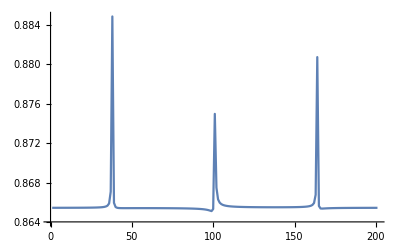

```mathematica
Clear[v,δc]
x1={};
v= m;
detun=100*10^6;
detstep=10^6;
velstep=1;
vellimit=300;
m=-vellimit;
While[m≤vellimit,
table2=ParallelTable[{δc,Abs[Γ/(Rph caj)Im[NSolve[eq1,Flatten[r]][[1,10,2]]]+ Γ/(Rpl cal) Im[NSolve[eq1,Flatten[r]][[1,12,2]]]+Γ/(Rpl can) Im[NSolve[eq1,Flatten[r]][[1,14,2]]]+ Γ/(Rpl cbi)Im[NSolve[eq2,Flatten[r]][[1,25,2]]]+ Γ/(Rph cbk)  Im[NSolve[eq2,Flatten[r]][[1,27,2]]]+Γ/(Rpl cbm)Im[NSolve[eq2,Flatten[r]][[1,29,2]]]+ Γ/(Rph cbo)  Im[NSolve[eq2,Flatten[r]][[1,31,2]]]+ Γ/(Rpl ccj) Im[NSolve[eq3,Flatten[r]][[1,42,2]]]+ Γ/(Rpl ccn)Im[NSolve[eq3,Flatten[r]][[1,46,2]]]+ Γ/(Rph ccp)Im[NSolve[eq3,Flatten[r]][[1,48,2]]]]},{δc,-detun,detun,detstep}];
AppendTo[x1,table2];
m=m+velstep]
l1=Length[Table[i,{i,-vellimit,vellimit,velstep}]];
l2=Length[Table[i,{i,-detun,detun,detstep}]];
ew=Transpose[Table[Table[x1[[i,j,2]],{j,1,l2}],{i,1,l1}]];
t=Table[Table[i,{i,-vellimit,vellimit}],{l2}];
z={};
Table[ParallelTable[{t[[i,j]],ew[[i,j]]},{j,1,l1}],{i,1,l2}][[1]];
For[n=1,n≤ l2,n=n+1,AppendTo[z,Interpolation[Table[Table[{t[[i,j]],ew[[i,j]]},{j,1,l1}],{i,1,l2}][[n]],Method->"Spline"
]
]
]

ListLinePlot[ParallelTable[Exp[- NIntegrate[z[[i]][x]* MB[x],{x,-300,300},Method->"LocalAdaptive"]],{i,1,l2}],PlotRange->All]
```

```mathematica
d=Table[i,{i,-detun,detun,detstep}];
Table[{d[[i]],Exp[- NIntegrate[z[[i]][x]* MB[x],{x,-300,300},Method->"LocalAdaptive"]]},{i,1,l2}]
```

{{-100000000,0.86545},{-99000000,0.86545},{-98000000,0.865451},{-97000000,0.865451},{-96000000,0.865451},{-95000000,0.865451},{-94000000,0.865452},{-93000000,0.865452},{-92000000,0.865452},{-91000000,0.865452},{-90000000,0.865453},{-89000000,0.865453},{-88000000,0.865454},{-87000000,0.865454},{-86000000,0.865455},{-85000000,0.865455},{-84000000,0.865456},{-83000000,0.865457},{-82000000,0.865458},{-81000000,0.865459},{-80000000,0.86546},{-79000000,0.865461},{-78000000,0.865463},{-77000000,0.865465},{-76000000,0.865467},{-75000000,0.86547},{-74000000,0.865474},{-73000000,0.865478},{-72000000,0.865484},{-71000000,0.865491},{-70000000,0.865502},{-69000000,0.865517},{-68000000,0.865541},{-67000000,0.865582},{-66000000,0.865665},{-65000000,0.865891},{-64000000,0.867089},{-63000000,0.884875},{-62000000,0.865954},{-61000000,0.865526},{-60000000,0.865449},{-59000000,0.865426},{-58000000,0.865418},{-57000000,0.865415},{-56000000,0.865414},{-55000000,0.865414},{-54000000,0.865414},{-53000000,0.865414},{-52000000,0.865415},{-51000000,0.865415},{-50000000,0.865416},{-49000000,0.865416},{-48000000,0.865416},{-47000000,0.865416},{-46000000,0.865416},{-45000000,0.865416},{-44000000,0.865416},{-43000000,0.865416},{-42000000,0.865416},{-41000000,0.865416},{-40000000,0.865416},{-39000000,0.865415},{-38000000,0.865415},{-37000000,0.865414},{-36000000,0.865414},{-35000000,0.865413},{-34000000,0.865413},{-33000000,0.865412},{-32000000,0.865411},{-31000000,0.86541},{-30000000,0.865409},{-29000000,0.865408},{-28000000,0.865407},{-27000000,0.865406},{-26000000,0.865404},{-25000000,0.865403},{-24000000,0.865401},{-23000000,0.865399},{-22000000,0.865397},{-21000000,0.865395},{-20000000,0.865393},{-19000000,0.86539},{-18000000,0.865387},{-17000000,0.865383},{-16000000,0.86538},{-15000000,0.865375},{-14000000,0.86537},{-13000000,0.865365},{-12000000,0.865358},{-11000000,0.865351},{-10000000,0.865341},{-9000000,0.865331},{-8000000,0.865317},{-7000000,0.865301},{-6000000,0.86528},{-5000000,0.865253},{-4000000,0.865216},{-3000000,0.865167},{-2000000,0.865116},{-1000000,0.86533},{0,0.874986},{1000000,0.867489},{2000000,0.866303},{3000000,0.865972},{4000000,0.865824},{5000000,0.865741},{6000000,0.865688},{7000000,0.865652},{8000000,0.865626},{9000000,0.865605},{10000000,0.86559},{11000000,0.865577},{12000000,0.865567},{13000000,0.865558},{14000000,0.865551},{15000000,0.865545},{16000000,0.865539},{17000000,0.865535},{18000000,0.865531},{19000000,0.865527},{20000000,0.865524},{21000000,0.865521},{22000000,0.865519},{23000000,0.865516},{24000000,0.865515},{25000000,0.865513},{26000000,0.865511},{27000000,0.86551},{28000000,0.865509},{29000000,0.865508},{30000000,0.865507},{31000000,0.865506},{32000000,0.865505},{33000000,0.865505},{34000000,0.865504},{35000000,0.865504},{36000000,0.865504},{37000000,0.865504},{38000000,0.865504},{39000000,0.865504},{40000000,0.865504},{41000000,0.865505},{42000000,0.865505},{43000000,0.865506},{44000000,0.865507},{45000000,0.865508},{46000000,0.86551},{47000000,0.865512},{48000000,0.865514},{49000000,0.865516},{50000000,0.865519},{51000000,0.865523},{52000000,0.865528},{53000000,0.865534},{54000000,0.865541},{55000000,0.865551},{56000000,0.865564},{57000000,0.865582},{58000000,0.86561},{59000000,0.865654},{60000000,0.865737},{61000000,0.865934},{62000000,0.866772},{63000000,0.880749},{64000000,0.865636},{65000000,0.865383},{66000000,0.86537},{67000000,0.865378},{68000000,0.865388},{69000000,0.865397},{70000000,0.865404},{71000000,0.86541},{72000000,0.865414},{73000000,0.865418},{74000000,0.865422},{75000000,0.865425},{76000000,0.865427},{77000000,0.865429},{78000000,0.865431},{79000000,0.865433},{80000000,0.865435},{81000000,0.865436},{82000000,0.865437},{83000000,0.865438},{84000000,0.865439},{85000000,0.86544},{86000000,0.865441},{87000000,0.865441},{88000000,0.865442},{89000000,0.865443},{90000000,0.865443},{91000000,0.865444},{92000000,0.865444},{93000000,0.865445},{94000000,0.865445},{95000000,0.865445},{96000000,0.865446},{97000000,0.865446},{98000000,0.865446},{99000000,0.865447},{100000000,0.865447}}